## Rotational energies - data fit

```mathematica
Erot[I_,A_,B_]:=A*I*(I+1)-B*I^2(I+1)^2;
EVMI[I_,C_,J_,J0_]:=1/2 C(J-J0)^2+1/2(I(I+1)/J);
```

```mathematica
Spins1=Table[i+1/2,{i,1,13,2}];
Spins2=Table[i+1/2,{i,2,14,2}];
```

```mathematica
plotter[A_,B_]:=ListPlot[Table[{Spins1[[i]],Erot[Spins1[[i]],A,B]},{i,1,Length[Spins1]}],Joined->True];
```

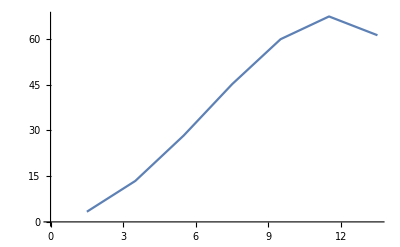

```mathematica
plotter[0.9,0.003]
```